```mathematica
rbar[r_,k_,t_]:=Mod[ModularInverse[k,t]*r,t,1]
```

```mathematica
secondOrder[r_,k_,t_]:=PolyGamma[rbar[r,k,t]/t]/k-PolyGamma[r/t];
```

```mathematica
SortEm[k_,t_]:=Module[{table, minfixed,i, j},
minfixed = Floor[Sqrt[k]];
table=Sort[Table[{N[-secondOrder[r, k, t]], r}, {r, minfixed, t}]];
table=Map[Part[#1,2]&,table];
i=minfixed;
j=1;
While[i<=t,
If[!table[[j]]==i,Break[]];
i++;
j++;
];
Return[Drop[table, j-1]]
]
```

```mathematica
SortEmAll[k_,t_]:=Module[{lst},lst=SortEm[k,t];If[lst==List[],Range[1,t],Join[Range[1,Min[lst]-1],lst]]]
```

```mathematica
PlotEm[k_,t_,opts:OptionsPattern[ListPlot]]:=ListPlot[Table[{r/t,secondOrder[r,k,t]},{r,1,t}],opts];
```

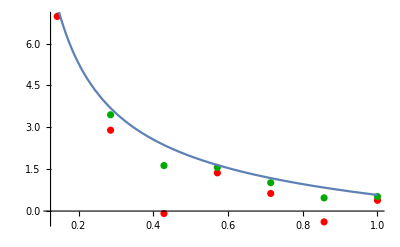

-Graphics-

```mathematica
Show[PlotEm[3,7,PlotRange->All,PlotStyle->Red],PlotEm[10,7,PlotRange->All,PlotStyle->Darker[Green]],Plot[-PolyGamma[x],{x,0,1}]]
```

```mathematica
SortEmAll[40, 11]
```

{1,2,3,4,5,6,7,8,9,10,11}

```mathematica
Needed[t_]:=Ceiling[6/Pi^2*(t^2-1)]
```

```mathematica
AllOrderingsLabeled[t_]:=Table[If[CoprimeQ[k,t],{k,SortEm[k,t]},Nothing],{k,2,Needed[t]+1}]
```

```mathematica
AllOrderings[t_]:=Module[{table},DeleteDuplicates[Table[If[CoprimeQ[k,t],SortEm[k,t],Sequence[]],{k,2,Needed[t]+1}]]]
```

```mathematica
AllOrderingsLabeled[9]
```

{{2,{3,5,7,9,2,4,6,8}},{4,{5,6,7,9,4,8}},{5,{6,7,8,9,5}},{7,{6,5,8,9,7}},{8,{9,7,8}},{10,{}},{11,{}},{13,{5,4,6,7,9,8}},{14,{6,5,7,8,9}},{16,{8,9,7}},{17,{9,8}},{19,{}},{20,{}},{22,{}},{23,{}},{25,{8,7,9}},{26,{9,8}},{28,{}},{29,{}},{31,{}},{32,{}},{34,{}},{35,{9,8}},{37,{}},{38,{}},{40,{}},{41,{}},{43,{}},{44,{9,8}},{46,{}},{47,{}},{49,{}},{50,{}}}

```mathematica
NumOrderings[t_]:=NumOrderings[t]=Length[AllOrderings[t]];
```

```mathematica
MaxOrdering[t_]:=MaxOrdering[t]=Module[{maxFound},
maxFound=2;
For[i=2,i<=Needed[t],i++,If[CoprimeQ[i,t]&&SortEm[i,t]≠{},maxFound=i,09]];
Return[maxFound];
]
```

```mathematica
WeirdOrderings[t_]:=Quiet[Select[AllOrderingsLabeled[t],#1[[2]]≠{}&]];
```

```mathematica
WhatGivesWeird[t_]:=Map[First,WeirdOrderings[t]];
```

```mathematica
WhatGivesWeird[9]
```

{2,4,5,7,8,13,14,16,17,25,26,35,44}

```mathematica
maxOrdering=Table[{t,MaxOrdering[t]},{t,2,10}];
```

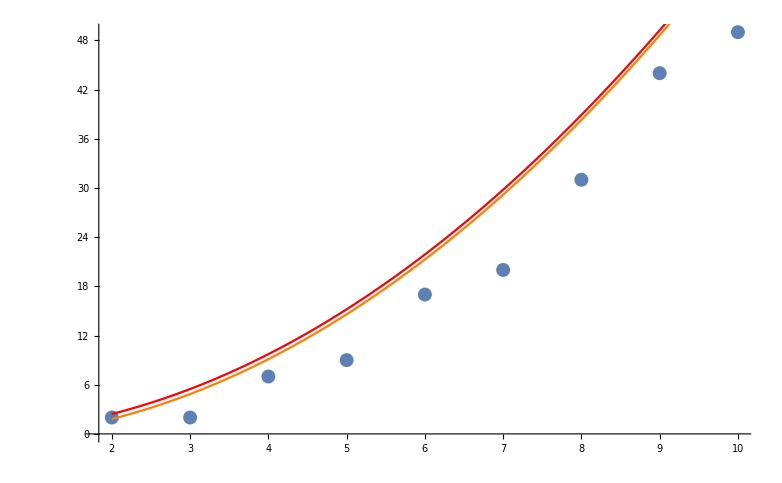

```mathematica
Show[ListPlot[maxOrdering],Plot[{6/Pi^2*(t^2-1),6/Pi^2*t^2},{t,2,10},PlotStyle->{Orange,Red}]]
```

```mathematica
KSOfClass[k_,t_]:=Select[Table[m*t+k,{m,0,Ceiling[Needed[t]/t]}],#1<=Needed[t]&]
```

```mathematica
KSInClasses[t_]:=Table[KSOfClass[k,t],{k,1,t}]
```

```mathematica
KSInClasses[7]
```

{{1,8,15,22,29},{2,9,16,23,30},{3,10,17,24},{4,11,18,25},{5,12,19,26},{6,13,20,27},{7,14,21,28}}

```mathematica
IsMore[r_,s_,k_,t_]:=N[secondOrder[r,k,t]]>N[secondOrder[s,k,t]]
```

```mathematica
Switcher[k_,t_,r_,s_]:=Map[IsMore[r,s,#1,t]&,KSOfClass[k,t]]
```

```mathematica
SwitcherWithIndex[k_,t_,r_,s_]:=Map[{#1,IsMore[r,s,#1,t]}&,KSOfClass[k,t]]
```

```mathematica
SwitcherWithIndex[6,7,6,7]
```

{{6,False},{13,False},{20,False},{27,True}}

{{6,False},{13,False},{20,False},{27,True}}

{{6,False},{13,False},{20,False},{27,True}}

```mathematica
FindSwitch[lst_]:=Table[If[lst[[i]][[2]]≠lst[[i-1]][[2]],{lst[[i]][[1]],lst[[i]][[2]]},Nothing],{i,2,Length[lst]}]
```

```mathematica
AllSwitches[k_,t_]:=Select[Flatten[Table[{r,s,SwitcherWithIndex[k,t,r,s]},{r,1,t},{s,r+1,t}],1],#1≠List[]&]
```

```mathematica
FindSwitch[{{1,True},{2,False}}]
```

{{2,False}}

FindSwitch[{{1,True},{2,False}}]

{{2,False}}

{{2,False}}

```mathematica
AllSwitches[6,7][[2]]
```

{1,3,{{6,True},{13,True},{20,True},{27,True}}}

```mathematica
GetSwitches[k_,t_]:=GetSwitches[k,t]=Select[Map[{#1[[1]],#1[[2]],Map[Floor[#1[[1]]/t]&,FindSwitch[#1[[3]]]]}&,AllSwitches[k,t]],#1[[3]]≠List[]&]
```

```mathematica
Clear[GetSwitches]
```

```mathematica
GetMoreSwitches[t_]:=Table[If[GCD[k,t]==1,{k,GetSwitches[k,t]},Nothing],{k,2,t-1}]
```

```mathematica
GetMoreSwitches[40];
```

```mathematica
GetAllSwitchPoints[t_]:=GetAllSwitchPoints[t]=Map[{#1[[1]],Sort[DeleteDuplicates[Map[Function[{a},a[[3]][[1]]],#1[[2]]]]]}&,GetMoreSwitches[t]]
```

```mathematica
GetAllSwitchPoints[53]
```

{{2,{1}},{3,{1,2}},{4,{1,2,3}},{5,{1,2,3}},{6,{1,2}},{7,{1,2,3,4}},{8,{1,2,3,4}},{9,{1,2,3}},{10,{1,2,3,4,5}},{11,{1,2,3,4,5,6}},{12,{1,2,3,5,6,7}},{13,{1,2,3,4,6,7,8}},{14,{1,2,3,4,6,7}},{15,{1,2,3,4,5,7,9}},{16,{1,2,3,4,7,8}},{17,{1,2,3,4,5,8,10}},{18,{1,2,3,4,6}},{19,{1,2,3,4,5,6,9}},{20,{1,2,3,4,5,6,9}},{21,{1,2,3,4,6,8,12}},{22,{1,2,3,4,6,8,12}},{23,{1,2,3,4,5,9,13}},{24,{1,2,3,5,6,7,9,14}},{25,{1,2,3,4,5,6,7,10,14}},{26,{1,2,3,4,6,11,16}},{27,{1,2,3,5,8}},{28,{1,2,3,5,6,12}},{29,{1,2,3,4,6,12}},{30,{1,2,3,4,6,7,13}},{31,{1,2,3,4,5,6,7,13}},{32,{1,2,3,4,5,7,13}},{33,{1,2,3,4,5,8,9,16}},{34,{1,2,3,4,5,8,9,16}},{35,{1,2,3,4,6,9,10,17}},{36,{1,2,3,4,6,7,18}},{37,{1,2,3,4,5,6,9,19}},{38,{1,2,3,4,5,6,9,17}},{39,{1,2,3,4,5,7,10,20}},{40,{1,2,3,4,5,7,10,17}},{41,{1,2,3,4,6,7,11,21}},{42,{1,2,3,4,5,6,7,11,22}},{43,{1,2,3,4,5,6,7,11,23}},{44,{1,2,3,4,5,6,8,12,24}},{45,{1,2,3,4,6,8,9,12,25}},{46,{1,2,3,4,5,6,9,13,25}},{47,{1,2,3,5,6,9,11,13,27}},{48,{1,2,3,6,7,8,11,14,27}},{49,{1,2,3,4,6,7,9,11,14,27}},{50,{1,2,3,5,6,8,10,13,14,29}},{51,{1,2,3,4,5,8,13,15,30}},{52,{1,3,7,31}}}

```mathematica
GetAllSwitchPoints[10]
```

{{3,{}},{7,{}},{9,{}}}

```mathematica
GetAllSwitchPoints[11]
```

{{2,{}},{3,{}},{4,{}},{5,{}},{6,{}},{7,{}},{8,{}},{9,{}},{10,{}}}

```mathematica
GetAllSwitchPoints[16]
```

{{3,{}},{5,{}},{7,{}},{9,{}},{11,{}},{13,{}},{15,{}}}

```mathematica
AvgNumSwitchPoints[t_]:=AvgNumSwitchPoints[t]=N[Mean[Map[Length[#1[[2]]]&,GetAllSwitchPoints[t]]]]
```

```mathematica
MaxNumSwitchPoints[t_]:=MaxNumSwitchPoints[t]=N[Max[Map[Length[#1[[2]]]&,GetAllSwitchPoints[t]]]]
```

```mathematica
ListNumSwitch=Table[{t,MaxNumSwitchPoints[t]},{t,3,41}]
```

{{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.},{16,0.},{17,0.},{18,0.},{19,0.},{20,0.},{21,0.},{22,0.},{23,0.},{24,0.},{25,0.},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.},{31,0.},{32,0.},{33,0.},{34,0.},{35,0.},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.}}

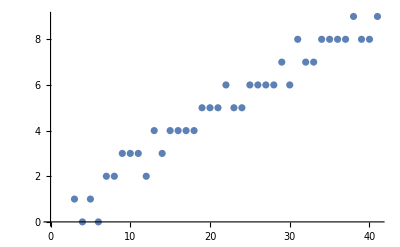

```mathematica
Show[ListPlot[ListNumSwitch]]
```

```mathematica
N[41/4]
```

10.25

```mathematica
(31^30)
```

550618520345910837374536871905139185678862401

```mathematica
SortEmAll[3,16]
```

{1,2,4,5,7,8,10,13,11,16,14,3,6,9,12,15}

```mathematica
SortEmAll[19,16]
```

{1,2,3,4,5,6,7,8,10,9,11,13,12,14,16,15}

```mathematica
SortEmAll[35,16]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}